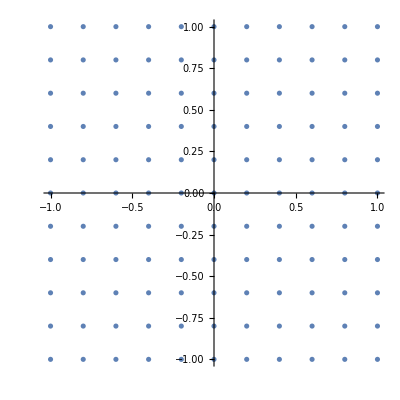

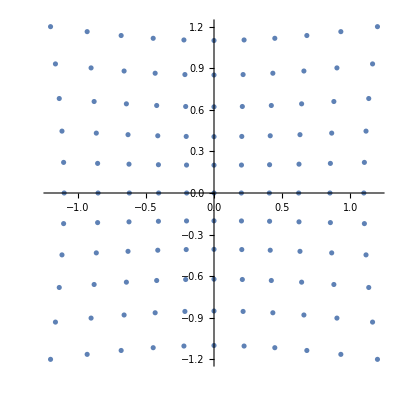

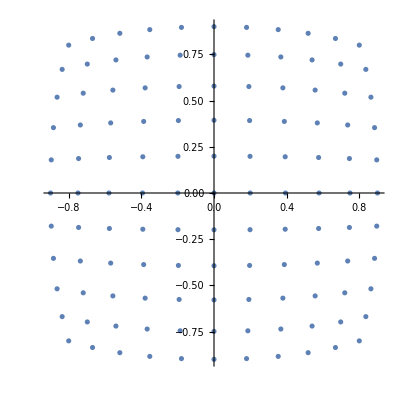

```mathematica
linear=Flatten[Table[{x, y},{x,-1,1,0.2},{y,-1,1,0.2}],1];
ListPlot[linear, AspectRatio->1]
d[r_, k_]:=r*(1+k*(r[[1]]^2+r[[2]]^2));
pillow=Table[d[linear[[i]],0.1],{i,1,Length@linear}];
ListPlot[pillow, AspectRatio->1]
barrel=Table[d[linear[[i]],-0.1],{i,1,Length@linear}];
ListPlot[barrel, AspectRatio->1]
```

```mathematica
dataExport=Join[{{"x", "y", "x_pillow", "y_pillow", "x_barrel", "y_barrel"}},SetPrecision[Join[linear,pillow,barrel,2],5]];
file=Export[FileNameJoin[{NotebookDirectory[],"..","data","distorsion-types.txt"}],dataExport,"Table"];
```